```mathematica
两环产生的电场,上环带正电,下环带负电
```

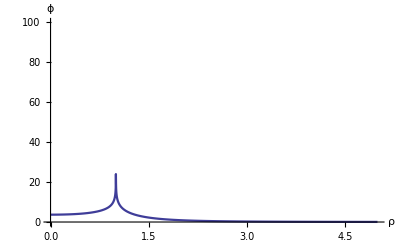

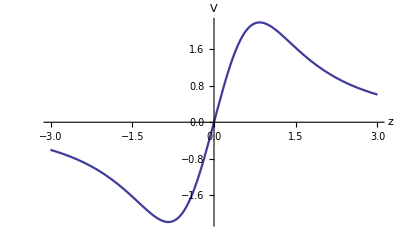

{2.19089,{z→0.837619}}

{-2.19089,{z→-0.837619}}

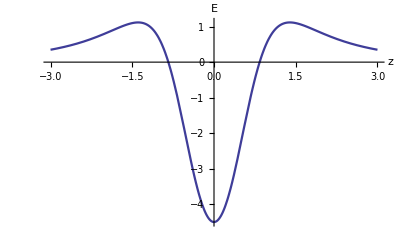

-Graphics3D-

```mathematica
V0[z_,ρ_]:=(2EllipticK[-(2R*ρ)/(z^2+(R-ρ)^2)])/(√(z^2+(R-ρ)^2))+
(2EllipticK[(2R*ρ)/(z^2+(R+ρ)^2)])/(√(z^2+(R+ρ)^2));R=1;d=R;
V1[z_,ρ_]:=V0[z-d/2,ρ];V2[z_,ρ_]:=-V0[z+d/2,ρ];
V[z_,ρ_]:=V1[z,ρ]+V2[z,ρ];
ϕ[ρ_]:=V[d/2,ρ]-V[-d/2,ρ];
Plot[ϕ[ρ],{ρ,0,5R},PlotRange->{{0,5R},{0,100}},
AxesOrigin->{0,0},AxesLabel->{"ρ","ϕ"},
AxesStyle->Thickness[0.003],
PlotStyle->Thickness[0.004]]
Plot[V[z,0],{z,-3R,3R},PlotRange->All,
AxesLabel->{"z","V"},AxesStyle->Thickness[0.003],
PlotStyle->Thickness[0.004]]
FindMaximum[V[z,0],{z,R}]
FindMinimum[V[z,0],{z,-R}]
field=-D[V[z,0],z];
Plot[field,{z,-3R,3R},PlotRange->All,
AxesLabel->{"z","E"},AxesStyle->Thickness[0.003],
PlotStyle->Thickness[0.004]]
Plot3D[V[z,ρ],{z,-3R,3R},{ρ,0,2R},
PlotRange->All,PlotPoints->50,
AxesLabel->{"z","ρ","V"},
AxesStyle->Thickness[0.003],
PlotStyle->Thickness[0.004]]
Clear[R,d,z,ρ,V,V0,V1,V2,field,ϕ]
```